```mathematica
vv:={aa,aa,aa,aa,aa,bb,bb,bb,bb,bb,"+","-","×","÷"};
```

```mathematica
vv={1,2,3,4,5,6,7,8,9,"+","-","×","÷"};
```

```mathematica
reset[nn_,mm_,oo_]:=Module[{},
aa=Random[Integer,{1,9}];
bb=Random[Integer,{1,9}];
While[aa==bb,bb=Random[Integer,{1,9}]];
For[x=2,x≤nn+mm,x++,
For[y=2,y≤mm+oo,y++,
v[x,y]=vv[[Random[Integer,{1,14}]]]]];
x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}];
While[x-y<1-oo||x-y>nn-1,x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}]];
v[x,y]="=";]
```

```mathematica
reset[nn_,mm_,oo_]:=Module[{},For[x=2,x≤nn+mm,x++,
For[y=2,y≤mm+oo,y++,
v[x,y]=vv[[Random[Integer,{1,13}]]]]];
x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}];
While[x-y<1-oo||x-y>nn-1,x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}]];
v[x,y]="=";]
```

```mathematica
reset[nn_,mm_,oo_]:=Module[{},For[x=2,x≤nn+mm,x++,
For[y=2,y≤mm+oo,y++,
v[x,y]=vv[[Random[Integer,{1,13}]]]]];
Do[x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}];
While[x-y<1-oo||x-y>nn-1||v[x,y]=="=",x=Random[Integer,{2,nn+mm}];y=Random[Integer,{2,mm+oo}]];
v[x,y]="=",{2}]]
```

```mathematica
p[x_,y_]:={2Sqrt[3]/2 x-y Sqrt[3]/2,1.5y }
p[{x_,y_}]:=p[x,y]

board[nn_,mm_]:={Table[hex[i,j],{j,2,mm+1},{i,2,nn-1+j}],
	Table[hex[i,j],{j,mm+2,nn+mm},{i,j-mm+1,nn+mm}]}

hex[x_,y_]:={
	Line[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}],Text[StyleForm[v[x,y],FontSize->30],p[x,y]-{0,.05}]}
```

```mathematica
board[nn_,mm_,oo_]:=Map[hex[#[[1]],#[[2]]]&,Select[Flatten[Table[{i,j},{i,2,nn+mm},{j,2,mm+oo}],1],1-oo≤ #[[1]]-#[[2]]≤ nn-1&]]
```

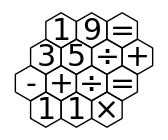

```mathematica
reset[3,3,2];
Graphics[{board[3,3,2]},AspectRatio->Automatic]
```

```mathematica
box[nn_,mm_,oo_]:=Module[{},
B1=Map[v[#[[1]],#[[2]]]&,B,{2}];
B2=Map[simple[#,nn,mm,oo]&,B1];
B3=Map[crash,B2];
	If[Count[B3,True]==1,
pos=Position[B3,True][[1,1]];
B4=B[[pos]];
				pic1=Graphics[{board[nn,mm,oo],Text[" ",{nn+1/2,1}]}];
				pic2=Graphics[{AbsoluteThickness[2],Text[StyleForm[Apply[StringJoin,Map[ToString,B2[[pos]]]],FontSize->20],{nn+1/2,1}],RGBColor[.5,.5,1],Line[Map[p[#]&,B4]]}];
				p1=Show[pic1,AspectRatio->Automatic,ImageSize->{35(2n-1),35(2n-1)},DisplayFunction->Identity];
			p2=Show[{pic1,pic2},AspectRatio->Automatic,ImageSize->{35(2n-1),35(2n-1)},DisplayFunction->Identity,PlotRange->All];
		Show[GraphicsArray[{p1,p2},DisplayFunction->$DisplayFunction,ImageSize->{100(nn+mm/2),50(mm+oo)}]]]]
```

```mathematica
chec[nn_,mm_,oo_]:=Module[{},
		A=Table[If[i==1||i==nn+mm+1||j==1||j==mm+oo+1||i-j<1-oo||i-j>nn-1,1,0],{i,nn+mm+1},{j,mm+oo+1}];
B={};
		stack=Map[{#}&,Position[A,0]];
    While[Length[stack]>0,
			path=Last[stack];
			stack=Drop[stack,-1];
			last=Last[path];
			nbrs=Select[{last+{1,0},last+{0,1},last+{-1,0},last+{0,-1},last+{1,1},last+{-1,-1}},!MemberQ[path,#]&&A[[Apply[Sequence,#]]]==0&];
			If[Length[nbrs]==0,If[Length[path]==Length[Position[A,0]],AppendTo[B,path]]];
			stack=Join[stack,Map[Join[path,f[last,#]]&,nbrs]]];
B]
```

```mathematica
f[a_,b_]:={b}
```

```mathematica
simple[L_,nn_,mm_,oo_]:=Module[{},
LL={};
If[Length[Select[Partition[L,2,1],0<=#[[1]]≤9||0<=#[[2]]≤9&]]<Which[nn==3&&mm==3&&oo==3,18,nn==3&&mm==3,13,nn==2&&mm==2,6,True,9],{0,"=",1},If[NumberQ[First[L]]&&NumberQ[Last[L]],L,{0,"=",1}]]]
```

```mathematica
dtn[L_]:=Fold[10#1+#2&,0,L]
```

```mathematica
crash[L_]:=ToExpression[Apply[StringJoin,Map[ToString,L//."="->"=="]]]
```

```mathematica
temp[3,3,3]=chec[3,3,3];
```

```mathematica
temp[3,3,2]=chec[3,3,2];
```

```mathematica
temp[3,2,2]=check[3,2,2];
```

```mathematica
temp[2,2,2]=check[2,2,2];
```

```mathematica
B=chec[3,2,2];
For[try=1,try≤10000000,try++,
reset[3,2,2];
box[3,2,2]]
```

## 3x2x2

## 3x3x2

## 3x3x3

## best